```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA"}]]
```

Successfully patched FeynArts.

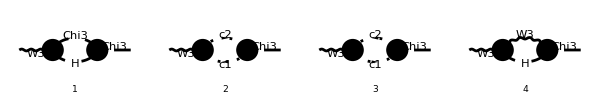

```mathematica
LoopDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],V[3] -> S[4], InsertionLevel->{Particles},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA", "Photonless_Weak_gaugeonly_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA", "Photonless_Weak_gaugeonly_FA"}]];
Paint[LoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{6,1},ImageSize->{600,100}];
```

```mathematica
Const1[x_]:=1;
Const0[x_]:=0;
evalLoop[ex_]:=ex//TID[#,q,ToPaVe->True]&//DotSimplify[#,Expanding->False]&//DiracSimplify[#,DiracSubstitute67->True]&//Collect2[#,{A0,B0,C0,D0}]&;
processLoop[exs_]:=(
a1=FCTraceFactor/@DotSimplify[#,Expanding->False]&/@exs;
a2=evalLoop/@a1;
a3=Total[a2];
FCClearScalarProducts[];
Pair[Momentum[p1],Momentum[p1]]=s;
a4=ChangeDimension[PaXEvaluate[a3],4]//Expand
)
```

```mathematica
TotalLoop[0]=FCReplaceAll[#,{vH->2 mW/gW,lambda->mh^2 gW^2/(8 mW^2)}]&/@Contract/@FCFAConvert[CreateFeynAmp[LoopDiags,Truncated->False,PreFactor->1],IncomingMomenta->p,OutgoingMomenta->p,LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

```mathematica
TotalLoop[1]=TotalLoop[0]//processLoop//Collect2[#,1/Epsilon]&;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
TotalLoop[3]=(TotalLoop[2]/ⅈ)//Collect2[#,Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]],Head->h1]&//Collect2[#,Pair[LorentzIndex[Lor1],Momentum[p1]] ,Head->h2]&//Collect2[#,Pair[LorentzIndex[Lor2],Momentum[p1]] ,Head->h2]&//FCReplaceAll[ #,h1->Const1,h2->Const0]&//Expand;
```

```mathematica
TotalLoop[4]=TotalLoop[3]/.{gW->0.3,mW->1,mh->0.1};
```

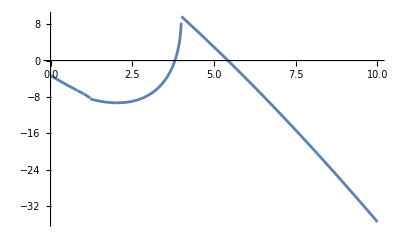

```mathematica
Plot[Re[TotalLoop[4]],{s,0,10}]
```

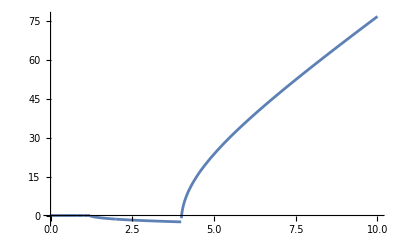

```mathematica
Plot[Im[TotalLoop[4]],{s,0,10}]
```

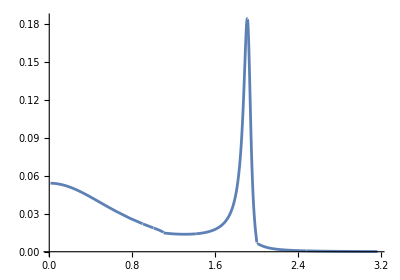

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+TotalLoop[4]]^-2},{s,0,10},PlotRange->Full],AspectRatio->0.7]
```